ElectroDynamics, by James Rohlf and Kevin Reiss, Version 2.0, Copyright 2022, All Rights Reserved.

__________________________________________________________________________________

Section | Magnetostatics

2.1 Charge Motion in a Uniform Field
	2.2 Steady Currents
	2.3 Law of Biot-Savart 
	2.4 Ampère's Law
	2.5 Vector Potential
	2.6 Comparing Electric and Magnetic Dipoles
	2.7 Expansion of A and the Magnetic Dipole
	2.8 Boundary Conditions
	2.9 Helmholtz Coils
	2.10 Summary of B, A, and J

Helmholtz coils produce a remarkably uniform field from a simple geometry as described in Section 2.7.

```mathematica
(Column[{#[EntityProperty["WolframDemonstration","WolframDemonstrationsLink"]]/.Hyperlink[link_]:>Hyperlink[#[EntityProperty["WolframDemonstration","Name"]],link],Row[{"By: "}~Join~Riffle[(Hyperlink[#["Name"],First[#["ContributorLink"]]])&/@#[EntityProperty["WolframDemonstration","Authors"]],", "]],ResourceData["Demonstrations Project: "<>#["Title"]]}]&)[Entity["WolframDemonstration","HelmholtzCoil"]]
```

[Helmholtz Coil ](https://demonstrations.wolfram.com/HelmholtzCoil)
By: [Thomas Koeppel](http://demonstrations.wolfram.com/author.html?author=Thomas+Koeppel)

Magnetostatics is the subject of magnetic fields, forces, and potential resulting from steady currents. A steady current is one that is not only constant in time but also uniform around some closed circuit.

The magnetic force differs fundamentally from the electric force in that there is no magnetic charge. This leads immediately to the second Maxwell equation. This is often referred to as Gauss’s law for magnetic fields.

∇ \[Application] B = 0

Magnetic field lines are closed loops. There is no monopole source for them to begin or end on. The right-hand-side, where the magnetic charge density would appear, is always zero.

Magnetic fields are produced by moving charges and other moving charges experience a magnetic force as the result of the field, the so-called Lorentz force.

Draw a picture of two moving charges.

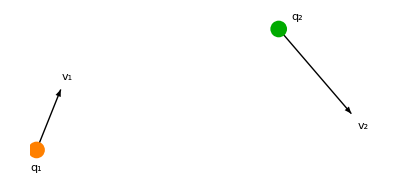

```mathematica
Graphics[{Style[Text[Subscript[q, 1],{0,-.15}],18],Style[Text[Subscript[q, 2],{2.15,1.1}],18],Arrow[{{0,0},{0.2,0.5}}],Style[Text[Subscript[v, 1],{.25,.6}],18],Arrow[{{2,1},{2.6,0.3}}],Style[Text[Subscript[v, 2],{2.7,.2}],18],Orange, PointSize[0.03],Point[{0,0}], Darker[Green], Point[{2,1}]}]
```

The force on q_2 is given by the Lorentz expression where the field is that caused by the source charge q_1.

F_2= q_2 v_2×B_1

A single moving charge is not a steady current. The magnetic field caused by q_1 is non-trivial unless it is nonrelativistic. The full expression for the magnetic field of a moving charge is derived in Chapter 9.

Comparison of the electric and magnetic terms in the Lorentz force expression indicates that the units of magnetic field, tesla (T), are the same as the units of the electric field divided by the velocity unit.

Show that 1 T = (1 V/m) / (1 m/s).

```mathematica
Quantity[, "Teslas"]==(Quantity[, "Volts"]/Quantity[, "Meters"])/Quantity[, ("Meters")/("Seconds")]
```

True

2.1 Charge Motion in a Uniform Field

A charged particle moving at right angles to a constant magnetic field exhibits uniform circular motion.

Draw the orbit of a charge moving at right angles to a magnetic field.

```mathematica
Show[Graphics3D[{Line[{{0,0,1},{1,0,1}}],Style[Text["e",{0,1,1.15}],16],Thickness[0.005],Arrow[{{0,0,1},{0,0,2}}],Style[Text["B",{.2,0,1.5}],18,Bold],Style[Text["R",{0.5,0,.9}],18,Bold],Arrow[{{0,1,1},{-.7,1,1}}],Style[Text["v",{-.3,1,1.1}],18,Bold],Darker[Green],Sphere[{0,1,1},.05]},Boxed->False],ParametricPlot3D[{Sin[t],Cos[t],1},{t,0,15},Axes->None, Ticks->None, Boxed->False]]
```

-Graphics3D-

Newton's law gives

e v B= (m v^2)/R

or in terms of momentum

p = e R B

Written this way, it has the advantage of being relativistically correct if the proper expression for momentum is used,

p= (m v^)/(√(1 - v^2/c^2))

Relativity is discussed in detail in Chap. 9. A useful unit of momentum is eV/c.

Calculate the radius of curvature of a 10 KeV/c electron in  a 1 mT field.

```mathematica
p = 10^4 Quantity[, ("Electronvolts")/("SpeedOfLight")]; B = 10^-3 Quantity[, "Teslas"];  N[UnitConvert[p/(Quantity[, "ElementaryCharge"]B)],2]
```

0.033 m

If the charged particle has a component of momentum parallel to the field, then the motion is helical.

```mathematica
Show[Graphics3D[{Style[Text["B",{0,0,5.2}],18,Bold],Thickness[0.01],Arrow[{{0,0,3},{0,0,5}}]},Boxed->False],ParametricPlot3D[{Cos[20 t],Sin[20 t],t},{t,2,4},Ticks->None]]
```

-Graphics3D-

If a perpendicular electric field is added with v ⊥ B, the motion is cycloidal. Interestingly, The net motion is not in the direction of E but perpendicular to both E and B.

```mathematica
Show[Graphics3D[{Thickness[0.005],Style[Text["E",{0,4.3,0}],18,Bold],Arrow[{{0,0,0},{0,4,0}}],Style[Text["B",{0,0,4.3}],18,Bold],Arrow[{{0,0,0},{0,0,4}}]},Boxed->False],ParametricPlot3D[{t-Sin[t],1-Cos[t],.1},{t,0,6Pi}]]
```

-Graphics3D-

The following demonstration allows exploration of the motion of a charged particle in electric and magnetic fields of arbitrary strength and direction.

```mathematica
(Column[{#[EntityProperty["WolframDemonstration","WolframDemonstrationsLink"]]/.Hyperlink[link_]:>Hyperlink[#[EntityProperty["WolframDemonstration","Name"]],link],Row[{"By: "}~Join~Riffle[(Hyperlink[#["Name"],First[#["ContributorLink"]]])&/@#[EntityProperty["WolframDemonstration","Authors"]],", "]],ResourceData["Demonstrations Project: "<>#["Title"]]}]&)[Entity["WolframDemonstration","ChargedParticleInUniformElectricAndMagneticFields"]]
```

[Charged Particle in Uniform Electric and Magnetic Fields ](https://demonstrations.wolfram.com/ChargedParticleInUniformElectricAndMagneticFields)
By: [Jeff Bryant](http://demonstrations.wolfram.com/author.html?author=Jeff+Bryant), [Michael Trott](http://demonstrations.wolfram.com/author.html?author=Michael+Trott), [Oleksandr Pavlyk](http://demonstrations.wolfram.com/author.html?author=Oleksandr+Pavlyk)

2.2 Steady Currents

A moving charge is a current which causes a magnetic field that makes a force that pushes nearby moving charges. A steady current consists of a group of charges moving together such that the charge density remains constant. The moving point charges above are obviously not a steady current.

The simplest steady current is that of a long line of charge, imagining that the circuit is closed at infinity. Every charge in the line moves at the same velocity. The current vector ℐ may be written in terms of the linear charge density λ and velocity v.

ℐ = λ v

For the purpose of comparison to the sheet and volume currents, take the line current to be in the x direction.

Draw a line of current.

```mathematica
Graphics3D[{Cylinder[{{0,0,0},{0,0,50}},1],Thickness[.01],Style[Text["ℐ",{4,2,25}],24,Bold],Arrow[{{1,2,10},{1,2,40}}]},Boxed->False]
```

-Graphics3D-

For a moving sheet of charge, a surface current may be written in terms of the surface charge density σ.

K = σ v

and

K=ℐ/y

where y corresponds to the direction perpendicular to the current.

Draw a sheet of current.

```mathematica
Graphics3D[{Table[Cylinder[{{0,2j,0},{0,2j,50}}],{j,1,10}],Thickness[.01],Arrow[{{2,11,10},{2,11,40}}],Style[Text["K",{1,7,25}],24,Bold]},Boxed->False]
```

-Graphics3D-

Draw a volume current.

A volume current may be written in terms of the volume charge density.

J = ρ v

and

J=K/z

```mathematica
Graphics3D[{Table[Table[Cylinder[{{2k,2j,0},{2k,2j,50}}],{j,1,10}],{k,1,10}],Thickness[.01],Arrow[{{0,11,10},{0,11,40}}],Style[Text["J",{1,12.5,25}],24,Bold]},Boxed->False]
```

-Graphics3D-

Note that all of the above currents (ℐ, K, J) can be made electrically neutral by superimposing positive and negative charges moving in opposite directions.

Four unique vectors are needed for the description of the field due to a current loop:

The position of a current element (r') along the current path.

The direction of the current along the current path.

The location 𝒫 where the magnetic field is being determined.

The vector that points from a current element to  𝒫 (r) along the current path.

```mathematica
Graphics3D[{Style[Text["ℐⅆ𝕝",{-1.1,1.3,.4}],16],Style[Text["𝒫",{2,1.05,1}],16,Bold],Style[Text["𝒪",{0,-.1,0}],16,Bold],Style[Text["ℛ",{.6,.9,.75}],16,Bold],Style[Text["r",{1,0.3,0.5}],16,Bold],Style[Text["r'",{-.6,0.4,.25}],16,Bold],Thickness[0.005],Arrow[{{0,0,0},{-1,1,.5}}],Arrow[{{0,0,0},{1.95,1,.95}}], Arrow[{{-1,1,.5},{1.9,1,1}}], Orange,Line[{{-1,1,0},{-1,1,1}}],Line[{{-1,1,1},{0,1,1}}],Line[{{0,1,1},{0,1,0}}],Line[{{0,1,0},{-1,1,0}}],Arrow[{{-.5,1,1},{-.4,1,1}}],Thickness[.015],Darker[Green],Arrow[{{-1,1,.4},{-1,1,.7}}]},Boxed->False]
```

-Graphics3D-

In addition we would need to know the velocity vector of a charge at 𝒫 to determine the magnetic force exerted on it.

2.3 Law of Biot-Savart

There is an experimentally determined expression that gives the contribution to the magnetic field due to a current element. A differential element of the magnetic field is

dB=(("μ")_0)/(4π)(ℐⅆ𝕝×ℛ)/ℛ^3

Since the current (ℐ) and the position vector that traces its path (𝕝) are in the same direction, then the scalar current ℐ times the differential vector ⅆ 𝕝 is the same as the vector current ℐ times the differential scalar ⅆ 𝕝.

ℐⅆ𝕝=ℐⅆ𝕝

By integrating, we get the Biot-Savart law which is the magnetic equivalent of Coulomb's law.

B=(("μ")_0)/(4π)∫(ℐⅆ𝕝'×ℛ)/ℛ^3=(("μ")_0)/(4π)∫(ℐ×ℛ)/ℛ^3 𝕕𝕝'

Normally, the integral will be around a closed loop but we also want to allow for the calculation of the contribution to the magnetic field due to any segment of the current. In terms of a surface current K or volume current J the Biot-Savart law is

B=(("μ")_0)/(4π)∫(K×ℛ)/ℛ^3 𝕕𝕒'

and

B=(("μ")_0)/(4π)∫(J×ℛ)/ℛ^3 𝕕𝕍'

In each case, the integration follows the path of the current specified by r' and integrates over the primed variable. The Biot-Savart law leads directly to ∇·B=0 using the vector ID for the divergence of a cross-product of arbitrary vectors 𝒜 and ℬ .

Verify that Div(𝒜×ℬ) =ℬ·Curl 𝒜- 𝒜·Curl ℬ.

```mathematica
𝒜={f[x,y,z],g[x,y,z],h[x,y,z]};ℬ={p[x,y,z],q[x,y,z],r[x,y,z]};Simplify[(𝒜×ℬ){x,y,z}==ℬ.𝒜{x,y,z}-𝒜.ℬ{x,y,z}]
```

True

Here 𝒜 = J and  ℬ=ℛ/ℛ^3. The vector J has no curl because it depends only on integration (primed) variables. The curl of ℛ/ℛ^3 is also zero.

Calculate the curl of ℛ/ℛ^3.

```mathematica
Curl[{(r-r')/(r-r')^3,0,0},{r,θ,ϕ},"Spherical"]
```

{0,0,0}

In index notation,

(∇×(r̂)/r^2)_k=ε_ijk∂_i [r_j(r_p r_p)^(-3/2)]=ε_ijk r_j∂_i (r_p r_p)^(-3/2)=ε_ijk r_j(-3/2)2 r_p∂_i r_p=ε_ijk(-3/r^5)r_i r_j=0

The last equality can be seen by switching i and j where ε_jik changes sign.

2.3.1 Moving Point Charges

The Biot-Savart law is strictly true only for steady currents. If we applied it to the force between 2 moving charges, we would get

F_2= q_2 v_2×B_1=(("μ")_0)/(4π)(q_2 q_1 v_2×( v_1×ℛ))/ℛ^3

It turns out that this formula is actually correct provided the charges are not relativistic (travelling significantly slower than  "c". To get a result that is in general relativistically correct, we may only apply the Biot-Savart law to steady currents. The relativistically correct formula which we shall derive in Chap. 9 is remarkably more sophisticated, representing the richness and sophistication of electrodynamics.

Calculate the magnetic force between the moving charges above, taking both charges to be  "e", the distance scale to be nm, and the speed scale to be 1/1000 "c".

```mathematica
v1=1/1000{0.2,0.5,0} Quantity[, "SpeedOfLight"];v2= 1/1000{0.6,-.7,0}Quantity[, "SpeedOfLight"]; ℛ=( {2,1,0}-{0,0,0})Quantity[, "Nanometers"];  UnitConvert[(Quantity[, "MagneticConstant"] Quantity[, "ElementaryCharge"]^2 v2×(v1×ℛ))/(4π (ℛ.ℛ)^(3/2)),Quantity[, ("Electronvolts")/("Meters")]]
```

{72.1248 eV/m,61.8213 eV/m,0. eV/m}

2.3.2 Straight Line Segment

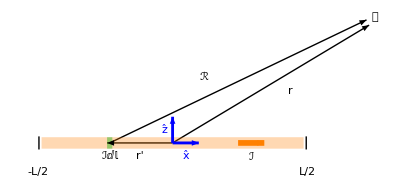

```mathematica
Graphics[{Line[{{-0.01,-0.025},{-0.01,0.025}}],Line[{{1+0.01,-0.025},{1+0.01,0.025}}],Style[Text["ℐ",{.8,-.055}],18,Bold ],Style[Text["r'",{0.375,-0.05}],18,Bold ],Style[Text["r",{.95,0.2}],18,Bold ],Style[Text["ℛ",{0.62,0.25}],18,Bold],Style[Text["𝒫",{1.27,0.48}],12],Style[Text["-L/2",{-.015,-0.11}],12],Style[Text["L/2",{1.015,-0.11}],12],Style[Text["ℐⅆ𝕝",{0.26,-0.05}],12],{{Orange,Thickness[0.01],Arrow[{{0.75,0},{0.85,0}}]},Arrow[{{0.5,0},{1.25,0.45}}],Arrow[{{0.26,0},{1.24,0.47}}],Arrow[{{.5,0},{.25,0}}]},Thickness[0.02],{Opacity[0.3],Orange,Line[{{0,0},{1,0}}]},{Thickness[0.005],Blue,Arrow[{{0.5,0},{0.5,0.1}}],Style[Text[x̂,{0.55,-0.05}],12],Style[Text[ẑ,{0.47,0.05}],12],Arrow[{{0.5,0},{0.6,0}}]},{Opacity[0.4],Darker[Green], Line[{{.25,0},{0.27,0}}]},Thickness[0.001],}]
```

Calculate the field at {x,0,z} due to a wire segment {-L/2,L/2}.

```mathematica
ClearAll["Global`*"]; $Assumptions={L>0,x′∈Reals,z>0,x>0};
r={x,0,z}; r′={x′,0,0};ℛ=r-r′; 
B=Subscript[μ, 0]/(4π)∫_(-L/2)^(L/2) (ℐ{1,0,0}×ℛ)/(ℛ.ℛ)^(3/2)ⅆx′//FullSimplify
```

{0,-((2 x (-1/(√((L-2 x)^2+4 z^2))+1/(√((L+2 x)^2+4 z^2)))+L (1/(√((L-2 x)^2+4 z^2))+1/(√((L+2 x)^2+4 z^2)))) ℐ μ_0)/(4 π z),0}

Examination of the form of B shows it may be written as

B=(("μ")_0ℐ)/(4π r)(sinθ_2-sinθ_1)

where θ is measured w.r.t the z-axis in the clockwise direction.

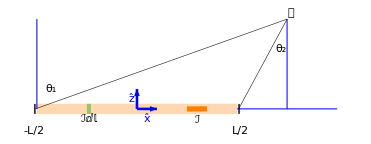

```mathematica
Graphics[{Line[{{-0.01,-0.025},{-0.01,0.025}}],Line[{{1+0.01,-0.025},{1+0.01,0.025}}],Style[Text["ℐ",{.8,-.055}],18,Bold ],Style[Text["𝒫",{1.27,0.48}],12],Style[Text["-L/2",{-.015,-0.11}],12],Style[Text["L/2",{1.015,-0.11}],12],Style[Text["ℐⅆ𝕝",{0.26,-0.05}],12],{{Orange,Thickness[0.01],Arrow[{{0.75,0},{0.85,0}}]},},Thickness[0.02],{Opacity[0.3],Orange,Line[{{0,0},{1,0}}]},{Thickness[0.002],Blue,Line[{{1,0},{1.5,0}}],Line[{{1.25,0.45},{1.25,0}}],Line[{{0,0},{0,.45}}]},{Thickness[0.005],Blue,Arrow[{{0.5,0},{0.5,0.1}}],Style[Text[x̂,{0.55,-0.05}],12],Style[Text[ẑ,{0.47,0.05}],12],Arrow[{{0.5,0},{0.6,0}}]},{Opacity[0.4],Darker[Green], Line[{{.25,0},{0.27,0}}]},Thickness[0.001],Line[{{-.008,0},{1.25,0.45}}],Style[Text[Subscript[θ, 1],{0.07,0.1}],14],Line[{{1.008,0},{1.25,0.45}}],Style[Text[Subscript[θ, 2],{1.22,0.3}],14]}]
```

Find the limit for a infinitely long wire.

```mathematica
Clear[r];Limit[B,L->∞]/. z->r//Quiet
```

{0,-(ℐ μ_0)/(2 π r),0}

One can readily check that the angle version written above gives the same answer for angles ± π/2.

The direction of the field may be verified by the right-hand-rule. Putting your thumb in the direction of the current, the magnetic field is in the direction of your curling fingers, e.g., -ŷ (out of the page) at 𝒫 in the drawing above.

Find the field at {x,y,z}.

```mathematica
ClearAll["Global`*"]; $Assumptions={L>0,x′∈Reals,z>0,x>0,y>0};
r={x,y,z}; r′={x′,0,0};ℛ=r-r′; 
B=Subscript[μ, 0]/(4π)∫_(-L/2)^(L/2) (ℐ{1,0,0}×ℛ)/(ℛ.ℛ)^(3/2)ⅆx′
```

{0,-(z (2 x (-1/(√((L-2 x)^2+4 (y^2+z^2)))+1/(√((L+2 x)^2+4 (y^2+z^2))))+L (1/(√((L-2 x)^2+4 (y^2+z^2)))+1/(√((L+2 x)^2+4 (y^2+z^2))))) ℐ μ_0)/(4 π (y^2+z^2)),(y (2 x (-1/(√((L-2 x)^2+4 (y^2+z^2)))+1/(√((L+2 x)^2+4 (y^2+z^2))))+L (1/(√((L-2 x)^2+4 (y^2+z^2)))+1/(√((L+2 x)^2+4 (y^2+z^2))))) ℐ μ_0)/(4 π (y^2+z^2))}

Calculate the field in the limit of an infinitely long wire.

```mathematica
g=Limit[B,L->∞]//Factor//Quiet
```

{0,-(z ℐ μ_0)/(2 π (y^2+z^2)),(y ℐ μ_0)/(2 π (y^2+z^2))}

Make a 2D plot of the field.

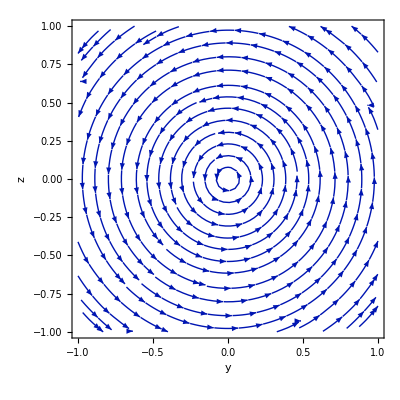

```mathematica
StreamPlot[g[[2;;3]]/.ℐ Subscript[μ, 0]->1,{y,-1,1},{z,-1,1},]
```

Make a 3D plot of the field.

```mathematica
Show[ StreamPlot3D[g/.ℐ Subscript[μ, 0]->1,{x,-1,1},{y,-1,1},{z,-1,1},StreamMarkers->"Arrow3D",AxesLabel->{x,y,z},ImageSize->Automatic],Graphics3D[{Arrow[{{-.25,0,0},{.25,0,0}}],,Arrow[{{-1.5,0,0},{1.5,0,0}}]}]]
```

-Graphics3D-

2.3.3 Square Current Loop

```mathematica
Graphics3D[{{Orange,Opacity[0.5],Thickness[.02],Line[{{-1,-1,0},{1,-1,0}}],Line[{{1,-1,0},{1,1,0}}],Line[{{1,1,0},{-1,1,0}}],Line[{{-1,1,0},{-1,-1,0}}]},Thickness[0.01],Arrow[{{0,0,0},{1,2,3}}],Style[Text["𝒫",{1.05,2.1,3.1}],14],Style[Text["r'",{.4,1.3,1.51}],18,Bold],Arrow[{{0,0,0},{Sqrt[1-.25^2],.25,0}}],Style[Text["r'",{.5,.4,0}],18,Bold],Arrow[{{Sqrt[1-.25^2],.25,0},{1.05,2,3}}],Style[Text["ℛ'",{1.2,1,1.5}],18,Bold],Arrow[{{-.2,-1,0},{.2,-1,0}}],Style[Text["ℐ",{0,-1.1,-.3}],18,Bold]},Boxed->False,ImageSize->Automatic]
```

-Graphics3D-

Calculate the field due to a square current loop.

```mathematica
ClearAll["Global`*"]; $Assumptions={L>0};
r={x,y,z}; BLine[r′_,dir_]:=With[{ℛ=r-r′,xy=r′[[dir]]},((#/.xy->L/2)-(#/.xy->-L/2))&[Subscript[μ, 0]/(4π)∫(ℐ UnitVector[3,dir]×ℛ)/(ℛ.ℛ)^(3/2)ⅆ(xy)]]; 
B=BLine[{L/2,y′,0},2]-BLine[{x′,L/2,0},1]-BLine[{-L/2,y′,0},2]+BLine[{x′,-L/2,0},1]//FullSimplify
```

{1/(2 √2 π)z ((-2 L+4 y)/(((L+2 x)^2+4 z^2) √(L^2+2 L (x-y)+2 (x^2+y^2+z^2)))+(2 (L+2 y))/(((L-2 x)^2+4 z^2) √(L^2+2 L (-x+y)+2 (x^2+y^2+z^2)))+(2 (L-2 y))/(((L-2 x)^2+4 z^2) √(L^2-2 L (x+y)+2 (x^2+y^2+z^2)))-(2 (L+2 y))/(((L+2 x)^2+4 z^2) √(L^2+2 L (x+y)+2 (x^2+y^2+z^2)))) ℐ μ_0,1/(2 √2 π)z ((2 (L+2 x))/(((L-2 y)^2+4 z^2) √(L^2+2 L (x-y)+2 (x^2+y^2+z^2)))+(-2 L+4 x)/(((L+2 y)^2+4 z^2) √(L^2+2 L (-x+y)+2 (x^2+y^2+z^2)))+(2 (L-2 x))/(((L-2 y)^2+4 z^2) √(L^2-2 L (x+y)+2 (x^2+y^2+z^2)))-(2 (L+2 x))/(((L+2 y)^2+4 z^2) √(L^2+2 L (x+y)+2 (x^2+y^2+z^2)))) ℐ μ_0,1/(4 √2 π)((2 (L+2 x) (L-2 y))/(((L+2 x)^2+4 z^2) √(L^2+2 L (x-y)+2 (x^2+y^2+z^2)))+(2 (L+2 x) (L-2 y))/(((L-2 y)^2+4 z^2) √(L^2+2 L (x-y)+2 (x^2+y^2+z^2)))+(2 (L-2 x) (L+2 y))/(((L-2 x)^2+4 z^2) √(L^2+2 L (-x+y)+2 (x^2+y^2+z^2)))+(2 (L-2 x) (L+2 y))/(((L+2 y)^2+4 z^2) √(L^2+2 L (-x+y)+2 (x^2+y^2+z^2)))+(2 (L-2 x) (L-2 y))/(((L-2 x)^2+4 z^2) √(L^2-2 L (x+y)+2 (x^2+y^2+z^2)))+(2 (L-2 x) (L-2 y))/(((L-2 y)^2+4 z^2) √(L^2-2 L (x+y)+2 (x^2+y^2+z^2)))+(2 (L+2 x) (L+2 y))/(((L+2 x)^2+4 z^2) √(L^2+2 L (x+y)+2 (x^2+y^2+z^2)))+(2 (L+2 x) (L+2 y))/(((L+2 y)^2+4 z^2) √(L^2+2 L (x+y)+2 (x^2+y^2+z^2)))) ℐ μ_0}

Calculate the divergence of B.

```mathematica
FullSimplify[Div[B,{x,y,z}]]
```

0

Calculate the field at the center of the square.

```mathematica
Limit[B,{x->0,y->0,z->0}]
```

{0,0,(2 √2 ℐ μ_0)/(L π)}

2.3.4 Polygon Current Loop

Consider the magnetic field at the center of a regular polygon. This may be conveniently written in terms of the angles, at the same time checking that it agrees with the brute force integration.

Calculate the magnetic field at the center of a square current loop of side L.

```mathematica
Clear[r];
4 (Subscript[μ, 0] ℐ)/(4π r)(Sin[θ2]-Sin[θ1])  /. {θ1->-π/4, θ2->π/4, r->L/2}
```

(2 √2 ℐ μ_0)/(L π)

The same technique gives the field at the center of an n-sided polygon, where the perpendicular distance from the center to any side is L / 2.

Calculate the field at the center of an n-sided polygon.

```mathematica
B=n(Subscript[μ, 0] ℐ)/(2π L)(Sin[θ2]-Sin[θ1])  /. {θ1->-π/n, θ2->π/n}
```

(n ℐ Sin[π/n] μ_0)/(L π)

Take the limit as n goes to infinity to get the answer for a circular loop.

```mathematica
Clear[r]; Limit[B,n->∞] /. L->2 r
```

(ℐ μ_0)/(2 r)

2.3.5 Circular Current Loop

The magnetic field due to a circular current loop (ring) along the axis of symmetry is a useful building block for other geometries of currents.

```mathematica
Show[Graphics3D[{Thickness[0.005],Arrow[{{0,0,1},{0,0,2.95}}],,Style[Text["R",{-.4,-0.4,0.8}],18],Style[Text["ẑ",{0,-0.1,1.14}],14],Style[Text["𝒫",{0,0,3.05}],14],Style[Text["ℛ",{0,.6,2}],18,Bold],Style[Text["r'",{0,.5,.9}],18,Bold],Style[Text["r",{0,-0.2,2}],18,Bold],Line[{{0,0,1},{0,0,2}}],Arrow[{{0,1,1},{0,.02,2.95}}],Thickness[.005],Thickness[0.005],Arrow[{{0,0,1},{0,0,1.3}}],Arrow[{{0,0,1},{0,1,1}}],Line[{{0,0,1},{-1/√5,-2/√5,1}}]},Boxed->False],ParametricPlot3D[{Sin[t],Cos[t],1},{t,0,15},Axes->None, Ticks->None, Boxed->False,PlotStyle->Orange]]
```

-Graphics3D-

Calculate the field due to a circular loop of radius R a distance z from the center along the symmetry axis.

```mathematica
ClearAll["Global`*"];
r={0,0,z}; r′=R{Cos[ϕ′],Sin[ϕ′],0};ℛ=r-r′; 
B=Subscript[μ, 0]/(4π)∫_0^(2π) R(ℐ{-Sin[ϕ′],Cos[ϕ′],0}×ℛ)/(ℛ.ℛ)^(3/2) ⅆϕ′
```

{0,0,(R^2 ℐ μ_0)/(2 (R^2+z^2)^(3/2))}

Calculate the magnetic field for R=0.2 "m", ℐ=1  "A", and z=.1  "m".

```mathematica
B[[1]]=0 Quantity[, "Teslas"]; B[[2]]=0 Quantity[, "Teslas"];UnitConvert[B,Quantity[, "Teslas"]]/. {R->0.2 Quantity[, "Meters"], ℐ->1 Quantity[, "Amperes"],z ->.1 Quantity[, "Meters"],Subscript[μ, 0]->Quantity[, "MagneticConstant"]}
```

{0 T,0 T,2.24794×10^-6 T}

2.3.6 Solenoid

We may build up a solenoid of current from rings.  The direction of B is along the axis of the solenoid and the contribution of one loop is given by

ⅆℐ = n ℐ ⅆz

```mathematica
$Assumptions={L>0,R>0}; B=∫_(-L/2)^(L/2) (R^2 n ℐ Subscript[μ, 0])/(2 (R^2+z′^2)^(3/2)) ⅆz′
```

(L n ℐ μ_0)/(√(L^2+4 R^2))

```mathematica
Show[Graphics3D[{Style[Text["z",{0,.2,4}],18,Bold],Style[Text["R",{.5,.15,3}],18],Style[Text["√(R^2)",{.5,-.2,4}],16],Line[{{.95,0,3},{0,0,5}}],Line[{{0,0,3},{.95,0,3}}],Thickness[0.01],Arrow[{{0,0,3},{0,0,5}}]},Boxed->False],ParametricPlot3D[{Cos[20 t],Sin[20 t],t},{t,2,4},Ticks->None]]
```

-Graphics3D-

Find the field for infinite length.

```mathematica
Limit[B,L->∞]//Quiet
```

n ℐ μ_0

2.3.7 Spinning Sphere of Charge

A spinning sphere of charge constitutes a surface current K. The field at the center may be calculated by dividing the sphere into rings. A differential piece of current is

ⅆℐ=K R ⅆθ  = σ v R ⅆθ =Q/(4 π R^2)ω R R sinθ

Divide a sphere into rings.

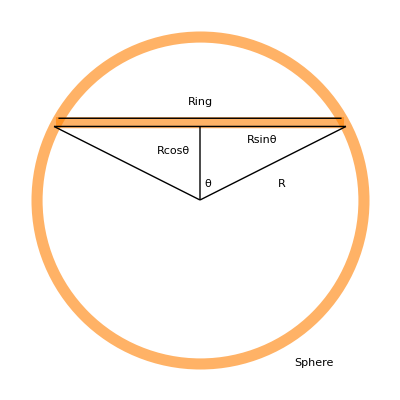

```mathematica
Graphics[{{Thickness[0.02],Opacity[0.6],Orange,Circle[],Line[{{-Sqrt[1-.473^2],.473},{Sqrt[1-.473^2],.473}}]},Line[{{-Sqrt[1-.5^2],.5},{Sqrt[1-.5^2],.5}}],Line[{{-Sqrt[1-.45^2],.45},{Sqrt[1-.45^2],.45}}],Line[{{0,0},{Sqrt[1-.45^2],.45}}],Line[{{-Sqrt[1-.45^2],.45},{0,0}}],Line[{{0,0},{0,.45}}],Style[Text["Ring",{0,.6}],14],Style[Text["Sphere",{.7,-1}],14],Style[Text["R",{.5,.1}],18],Style[Text["Rcosθ",{-.16,.3}],12],Style[Text["Rsinθ",{.38,.37}],12],Style[Text["θ",{.05,.1}],12]}]
```

Calculate the magnetic field at the center of a spinning sphere of charge.

```mathematica
$Assumptions={R>0};
B = (Subscript[μ, 0] Q ω)/((2)4 π)∫_0^π (R^2 Sin[θ]^3)/(((R Sin[θ])^2+(R Cos[θ])^2)^(3/2))ⅆθ
```

(Q ω μ_0)/(6 π R)

In 2.5 the field due to the spinning sphere will be calculated everywhere inside and outside using the vector potential.

2.4 Ampère’s Law

Ampère’s law can be derived from the Biot-Savart law, just as Gauss’s law is derivable from Coulomb’s law. The difference is that because of the vector nature of the magnetic force due to the non-existence of magnetic charge, the situation is more complicated. The source current (a vector) gives Curl(B), rather than the much simpler case of the source charge (a scalar) giving the Div(E).

The field for a long straight wire carrying a steady current drops as 1/r from the distance to the wire and its direction is  ϕ̂. The lines of B are observed to curl around the wire. Calculation of Curl(B), however, gives zero. What’s going on here?

Calculate Curl(1/r).

```mathematica
Clear[r]; Curl[1/r{0,1,0},{r,θ,ϕ},"Spherical"]
```

{0,0,0}

The situation is similar to that of the field due to a point charge which had zero divergence everywhere except at the location of the charge, resulting in a δ function. Here Curl(B) is zero everywhere except at r = 0, the location of the source where it is infinite for a line of current with zero size, again resulting in a δ  function. It’s Curl(B) at the actual source location that makes the field lines curl about the source, just as Div(E) at the source made the electric field lines diverge. In the electric case, we obtained a useful relationship (Gauss’s law) by integrating the diverges over a volume which cancelled the infinity from the δ function. This time, we are going to integrate the curl over surface area to cancel the δ function with the aid of Stoke’s theorem. In choosing the surface we want the boundary to follow the path of B so that we are able to easily do the line-integral resulting from Stoke’s theorem. A circular boundary does the job.

Draw a current segment and a surrounding surface over which to integrate Curl(B).

```mathematica
Graphics3D[{Orange,Thickness[0.01],Cylinder[{{-5,0,0},{5,0,0}},.3], Green,Opacity[.3],Cylinder[{{0,0,0},{0.001,0,0}},5],Opacity[1],Black,Arrow[{{0,2,2},{3,2,2}}],Style[Text["n̂",{3.3,2,2}],18,Bold],Arrow[{{5.3,0,0},{7.3,0,0}}],Style[Text["ℐ",{7.6,0,0}],18,Bold],Arrow[{{0,-5,0},{0,-5,-2}}],Style[Text["B",{0,-6,-1}],18,Bold]},Boxed->False]
```

-Graphics3D-

∫_S  (∇×B)\[Application] ⅆ𝕒=∮ B\[Application]ⅆ𝕝=2π r B = μ_0 ℐ_enc

The LHS is just the flux calculation of the curl, and is seen to be zero everywhere except where the curl penetrates the surface. The line integral is evaluated knowing the formula for B due to the long wire. There is a sign convention that is determined by the RHR. The line integral is positive when the unit vector points in the direction of the current. The surface dos not need to be 2-dimensional. One could, for example, take a hemisphere of the same radius. There are an infinite number of surfaces that have the same boundary as the simple circle.

The general result which we shall now prove is Ampères’s law.

∮ B\[Application]ⅆ𝕝= μ_0 ℐ_enc

In differential form it reads

∇×B= μ_0 J

since ℐ can be written as

ℐ=∫  J\[Application] ⅆ𝕒

It is seen geometrically, that the flux of Curl(B) is zero everywhere except where the current penetrates the surface. This is the 4th Maxwell equation but it is not yet complete, because like the expression for Curl(E), it needs modification for time-varying fields.

Make summary tables of the field equations for statics.

```mathematica
ClearAll["Global`*"];Row[{Dataset[AssociationThread[{"Operation","Result"},#]&/@{{"∫ E \[Application] ⅆ𝕒", Subscript[Q, in]/Subscript[ε, 0]},{"∮ E \[Application]  ⅆ𝕝",0},{"∫ B \[Application] ⅆ𝕒", 0},{"∮ B \[Application]  ⅆ𝕝",Subscript[μ, 0] Subscript[ℐ, enc]}},ItemSize->7],Dataset[AssociationThread[{"Operation","Result"},#]&/@{{"∇ \[Application]  E",ρ/Subscript[ε, 0]},{"∇ × E",0},{"∇ \[Application]  B", 0},{"∇ × B",Subscript[μ, 0] J}},ItemSize->7]},", "]
```

, ,

2.4.1 General derivation

To derive Ampère’s law for the general we need to take the curl of the Biot Savart law,

B=(("μ")_0)/(4π)∫(J×ℛ)/ℛ^3 ⅆ𝕍

leading to the curl of a cross product.

Verify that Curl(𝒜×ℬ)=(ℬ·Grad)𝒜 - (𝒜·Grad)ℬ + 𝒜Div ℬ - ℬDiv 𝒜.

```mathematica
𝒜={f[x,y,z],g[x,y,z],h[x,y,z]};ℬ={p[x,y,z],q[x,y,z],r[x,y,z]};Simplify[(𝒜×ℬ){x,y,z}==(ℬ⟦1⟧ D[𝒜, x]+ℬ⟦2⟧ D[𝒜, y]+ℬ⟦3⟧ D[𝒜, z])-(𝒜⟦1⟧ D[ℬ, x]+𝒜⟦2⟧ D[ℬ, y]+𝒜⟦3⟧ D[ℬ, z])+𝒜 ℬ{x,y,z}-ℬ 𝒜{x,y,z}]
```

True

We did something like this before when we took the divergence. Again 𝒜 = J and  ℬ=ℛ/ℛ^3. The vector J has no space derivatives because it depends only on integration variables so the first and the last terms are zero. The second term is also zero. Let’s look at it more closely. Remember everything is in the integrand with a volume integral over the primed coordinates. One can use a trick to allow integration by parts and that is to use the fact that

-∇ℛ/ℛ^3 = ∇' ℛ/ℛ^3

Another vector identity is needed.

Verify that Div(𝒶 𝒜) = 𝒶 Div(𝒜) + 𝒜·Grad(𝒶).

```mathematica
𝒶=s[x,y,z];Simplify[(𝒶 𝒜){x,y,z}==𝒶 𝒜{x,y,z}+𝒜.𝒶{x,y,z}]
```

True

In this identity 𝒜 = J and 𝒶 = ℛ_i/ℛ^3. We have for the i^th component

∫ J \[Application] ( ∇' ℛ_i/ℛ^3) ⅆ𝕍 =∫∇’\[Application](Jℛ_i/ℛ^3)ⅆ𝕍-∫ ℛ_i/ℛ^3∇'\[Application]J ⅆ𝕍

The last term is zero for a steady current. Using the divergence theorem, we may take the integration surface out to infinity so

∫∇’\[Application](Jℛ_i/ℛ^3)ⅆ𝕍=∫ℛ_i/ℛ^3J\[Application]ⅆ𝕒 = 0

There is but one term left.

∇×B=(("μ")_0)/(4π)∫J∇\[Application]ℛ/ℛ^3ⅆ𝕍=  ("μ")_0J

because

∇\[Application]ℛ/ℛ^3= 4π δ^3(ℛ)

2.4.2 Sheet of Current

Close to a sheet of current, the field is perpendicular to the surface current vector K.

Draw an Amperian loop for a current sheet.

```mathematica
Graphics3D[{Style[Text[B,{0.5,0.5,.2}],18,Bold],Style[Text[B,{0.5,0.5,-.2}],18,Bold],Style[Text[K,{0.5,0.5,.05}],18,Bold],Thickness[0.005],Arrow[{{.5,0.3,0},{.5,0.7,0}}],Arrow[{{.4,0.5,.15},{.6,0.5,.15}}],Arrow[{{.6,0.5,-.15},{.4,0.5,-.15}}],Thickness[0.01],Darker[Green], Line[{{0.3,0.5,.1},{0.7,0.5,.1}}], Line[{{0.7,0.5,.1},{.7,0.5,-.1}}],Line[{{.7,0.5,-.1},{0.3,0.5,-.1}}],Line[{{0.3,0.5,-.1},{0.3,0.5,.1}}],Orange, Opacity[0.3],Cuboid[{0,0,0},{1,1,0.001}]},Boxed->False]
```

-Graphics3D-

∮  B \[Application] ⅆ𝕝 =2L B=  ("μ")_0 ℐ_in=  ("μ")_0K L

B=(("μ")_0K)/2

Calculate the field for 10 A/m surface current.

```mathematica
K=10 Quantity[, "Amperes"]/Quantity[, "Meters"]; N[UnitConvert[(Quantity[, "MagneticConstant"]K)/2,Quantity[, "Teslas"]],2]
```

6.3×10^-6 T

2.4.3 Cylinder of Current

Consider a volume current with cylindrical cross section of radius R. Since the field is is azimuthal, we choose a circular integration path and consider two cases where the oath may be inside or outside the cylinder of current. Inside (r < R) we have

∮  B \[Application] ⅆ𝕝 =2π r B=  ("μ")_0 ℐ_enc=  ("μ")_0π r^2 J

B=(("μ")_0r J)/2

Outside (r > R)we have

∮  B \[Application] ⅆ𝕝 =2π r B=  ("μ")_0 ℐ_enc=  ("μ")_0π R^2 J

B=(("μ")_0 R^2 J)/(2 r)

Show the integration path for the cylinder.

```mathematica
Graphics3D[{Orange, Opacity[0.3],Cylinder[{{0,0,-3},{0,0,3}},.5],Darker[Green],Thickness[0.005],Opacity[.7],ResourceFunction["Circle3D"][{0,0,0},{1,1},π/2]},Boxed->False]
```

-Graphics3D-

2.4.4 Solenoid

W already calculate the field inside a long solenoid on the axis. Now we use Ampère’s law to get he field everywhere. Note that the solenoid is equivalent to a surface current along ϕ̂. The key to understanding the solenoid is that the direction of B is along the axis which is taken to be ẑ and that the field outside is zero. The field can have no radial component because if we change the direction of the current and turn it  upside down we get the same configuration. It can also have no azimuthal component because if we integrate B around a circle of constant z, there is no current enclosed (the current has no z component).

Draw the ϕ integration path.

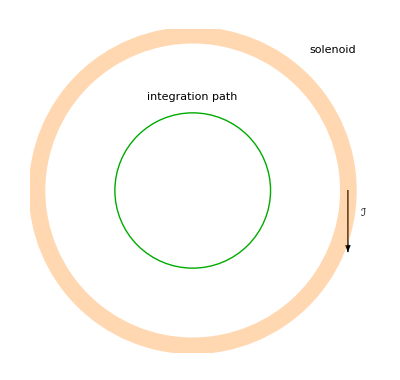

```mathematica
Graphics[{Style[Text[ℐ,{1.1,-.15}],14],Arrow[{{1,0},{1,-.4}}],Style[Text[solenoid,{.9,.9}],14],Style[Text[integration path,{0,.6}],14],Darker[Green],Circle[{0,0},.5],Orange, Thickness[0.03],Opacity[0.3],Circle[]}]
```

The field outside must be zero because if we take an rectangular loop at constant ϕ which is totally outside the solenoid, we get

∮  B \[Application] ⅆ𝕝 =B_1-B_2

so B is constant but since it goes to zero at infinity it must be zero everywhere.

Draw the  outside integration path.

```mathematica
Show[Graphics3D[{Thickness[.01],Darker[Green], Line[{{1,1,2},{1,1,3}}], Line[{{1,1,3},{2,2,3}}],Line[{{2,2,3},{2,2,2}}],Line[{{2,2,2},{1,1,2}}]},Boxed->False],ParametricPlot3D[{Cos[30 t],Sin[30 t],t},{t,0,5},Ticks->None]]
```

-Graphics3D-

Draw the integration path to compute B.

```mathematica
Show[Graphics3D[{Thickness[.01],Darker[Green], Line[{{1,1,2},{1,1,3}}], Line[{{1,1,3},{.2,.2,3}}],Line[{{.2,.2,3},{.2,.2,2}}],Line[{{.2,.2,2},{1,1,2}}]},Boxed->False],ParametricPlot3D[{Cos[30 t],Sin[30 t],t},{t,0,5},Ticks->None]]
```

-Graphics3D-

∮  B \[Application] ⅆ𝕝 = B L=  ("μ")_0 ℐ_enc=  ("μ")_0n L ℐ

B =  ("μ")_0n  ℐ

2.4.5 Toroid

A toroid has the shape or a solenoid bent into a circle. The key to understanding the toroid is that the direction of B is along ϕ̂, which follows from the fact that and that the current has no ϕ̂ component, and that the field outside is zero.

Draw the toroid.

```mathematica
Graphics3D[{Thickness[0.2],Opacity [.5], Orange,ResourceFunction["Circle3D"][{0,0,0},{1,1}], Darker[Green],Thickness[0.005],Opacity[1],ResourceFunction["Circle3D"][{0,0,0},{1,1}]},PlotRange-> All]
```

-Graphics3D-

Taking an integration path along ϕ̂, we have

∮  B \[Application] ⅆ𝕝 = B 2 π r=  ("μ")_0 ℐ_enc=  ("μ")_0N  ℐ

B = (("μ")_0N  ℐ)/(2 π r)

where N is the number of loops in the coil. The same calculation for the integration loop outside the toroid gives zero.

2.5 Vector Potential

The vector potential A plays a prominent role in electromagnetism. Since Div(B) = 0 we may define the vector potential as satisfying

B = ∇ × A

and we are free to choose Div(A) without effecting B. To see that this is true, if Div(A)≠0 then we could add to it a piece ∇^2 λ which makes Div(A)=0 by satisfying an equation identical to Poisson’s equation.  Compare with the electrostatic case of Curl(E) = 0 resulting in E = -Grad(V) and being free to chose the zero point of V.

Calculate the divergence of the curl of any vector.

```mathematica
𝒜={f[x,y,z],g[x,y,z],h[x,y,z]};(𝒜{x,y,z}){x,y,z}==(𝒜{x,y,z}){x,y,z}-𝒜{x,y,z}
```

True

Taking the curl of Ampère’s law,

∇×B=∇×(∇×A)=∇(∇\[Application]A)-∇^2 A= ("μ")_0J

and choosing Div(A)=0 we get

∇^2 A=- ("μ")_0J

This is just an equation for each component of A that is identical to Poisson’s equation.

∇^2 A_i=- ("μ")_0 J_i

The solution is

A_i=(("μ")_0)/(4π)∫J_i/ℛ ⅆ𝕍

Choosing the value of Div(A) is called a gauge condition and Div(A) = 0 is called the Coulomb gauge due to its solution being identical to the electrostatic problem.

2.5.1 Solenoid

The vector potential for a long solenoid is found with the aid of Stoke’s theorem. Integrate B across a disk of radius r. Inside we have

∫ B\[Application] ⅆ𝕒=∫ (∇×A)\[Application] ⅆ𝕒=∮  A \[Application] ⅆ𝕝

π r^2 B =π r^2  ("μ")_0n  ℐ=2π r A

A = (("μ")_0n  ℐ r)/2 ϕ̂

Check the answer by taking the curl.

```mathematica
Curl[1/2 (Subscript[μ, 0] n ℐ r) {0,1,0},{r,ϕ,z},"Cylindrical"]
```

{0,0,n ℐ μ_0}

Outside

π r^2 B =π R^2  ("μ")_0n  ℐ=2π r A

A = (("μ")_0n  ℐ R^2)/(2 r) ϕ̂

Check the answer by taking the curl.

```mathematica
Curl[(Subscript[μ, 0] n  ℐ R^2)/(2 r) {0,1,0},{r,ϕ,z},"Cylindrical"]
```

{0,0,0}

2.5.2  Sheet of Current

Consider a sheet of current. The vector potential is in the direction of the current (take to be x̂ and only depends on the direction perpendicular to the plane (ẑ) because  the magnetic field is along ±ŷ.

A=f(z) x̂

∇×A=-(∂ f)/(∂ z)ŷ =B=±(("μ")_0 K)/2 ŷ

Where B is in opposite directions on opposite sides of the sheet of charge.

A=±(("μ")_0 K z)/2 ŷ

We may add a constant to A without changing B.

2.5.3 Long Straight Current

We may get the vector potential from a current by direct integration. The vector potential due to a long straight wire of radius R carrying a steady current may be written

A=(("μ")_0)/(4π)∫ℐ/ℛ ⅆ𝕝

The vector potential is along the direction ẑ of the current and can only depend on r by symmetry. Therefore, we may express A as

A=f(r) ẑ

Outside the wire

∇×A=-(∂ f)/(∂ r)ϕ̂ =B=(("μ")_0 ℐ)/(2π r) ϕ̂

A=-(("μ")_0ℐ)/(2π)ln r/R  ẑ

Check the answer by taking the curl.

```mathematica
Curl[-(Subscript[μ, 0] ℐ)/(2π R^2) Log[r/R]{0,0,1},{r,ϕ,z},"Cylindrical"]
```

{0,(ℐ μ_0)/(2 π r R^2),0}

Inside the wire

∇×A=-(∂ f)/(∂ r)ϕ̂ =B=(("μ")_0 ℐ r)/(2π R^2) ϕ̂

A=-(("μ")_0ℐ)/(4π R^2)(r^2-R^2)  ẑ

Check the answer by taking the curl.

```mathematica
Curl[-(Subscript[μ, 0] ℐ)/(4π R^2)(r^2-R^2){0,0,1},{r,ϕ,z},"Cylindrical"]
```

{0,(r ℐ μ_0)/(2 π R^2),0}

2.5.4 Finite Line of Current

Consider a finite line of current along ẑ from a to b. Choose the origin of the coordinate system such that the field has only a radial  component.

Draw  the coordinates.

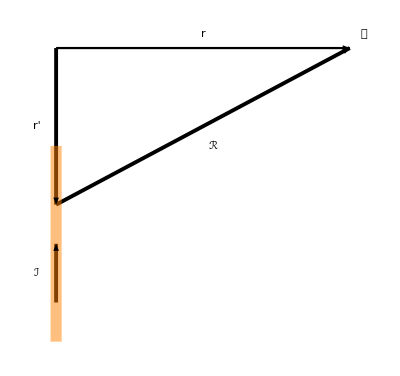

```mathematica
ClearAll["Global`*"];Graphics[{Thickness[0.004],Arrow[{{0,1.5},{1.5,1.5}}],Style[Text[r,{.75,1.57}],16,Bold],Thickness[0.007],Arrow[{{0,1.5},{0,.7}}],Style[Text[r',{-.1,1.1}],18,Bold],Arrow[{{0,.7},{1.5,1.5}}],Style[Text[ℛ,{.8,1}],18,Bold],Style[Text[𝒫,{1.57,1.57}],16],Arrow[{{0,.2},{0,.5}}],Style[Text[ℐ,{-.1,.35}],16,Bold],Orange, Opacity[0.5],Thickness[0.02],Line[{{0,0},{0,1}}]},Boxed->False]
```

Calculate the vector potential.

```mathematica
$Assumptions={r∈Reals, r>0,z∈Reals, 𝓏∈Reals};ℛ={r,0,0}-{0,0,𝓏}; f[𝓏_]=(Subscript[μ, 0] ℐ)/(4π)∫ 1/(√(ℛ.ℛ))ⅆ𝓏;  A=FullSimplify[f[b]-f[a]]
```

(ℐ (-ArcTanh[a/(√(a^2+r^2))]+ArcTanh[b/(√(b^2+r^2))]) μ_0)/(4 π)

Calculate the curl.

```mathematica
FullSimplify[Curl[A{0,0,1},{r,ϕ,z},"Cylindrical"]]
```

{0,((-a/(√(a^2+r^2))+b/(√(b^2+r^2))) ℐ μ_0)/(4 π r),0}

Calculate the divergence.

```mathematica
FullSimplify[Div[A {0,0,1},{r,ϕ,z},"Cylindrical"]]
```

0

2.5.5 Spinning Sphere of Charge

The example of a spinning sphere of charge will play an important role in the discussion of magnetic fields inside matter. It is worth the time to understand it thoroughly. A spinning sphere of charge constitutes a a non-uniform surface current.

K = σ v= σ R sinθ ω ϕ̂

The direction of the current is in along the phi angle ϕ̂ in the coordinate system where the polar angle is α. This choice of coordinates makes for a difficult integration. It is much easier to choose a coordinate system that is rotated by an angle α  such that the polar angle becomes the angle between r and r'. After integration, one can rotate back to the frame where ω points along ẑ.

Draw a diagram of the rotating sphere.

```mathematica
ClearAll["Global`*"];Graphics3D[{Style[Text[𝒫,{0,0,1.6}],16],Style[Text[ℛ,{.4,0,1.2}],18,Bold],,Style[Text[r',{.4,-.3,.3}],18,Bold],Style[Text[ω,{-.4,0,.3}],18,Bold],Style[Text[r,{-.1,0,0.8}],18,Bold],Style[Text[θ,{.1,0,.3}],16],Style[Text[α,{-.1,0,.3}],16],{Opacity[0.2],Orange,Sphere[]},Arrow[{{0,0,0},{0, 0, 1.5}}],Arrow[{{0,0,0},{-.6,0, Sqrt[1-.6^2]}}],Arrow[{{.6,-.6, Sqrt[1-.6^2]},{0,0,1.5}}],Arrow[{{0,0,0},{.6,-.6, Sqrt[1-.6^2]}}],{Thickness[0.005],Blue,Arrow[{{1.5,0,0},{1.5,0,.5}}],Style[Text[OverHat["z"],{1.5,0,.65}],12,Bold],Style[Text[OverHat["x"],{2.15,0,0}],12,Bold],Arrow[{{1.5,0,0},{2,0,0}}],Style[Text[OverHat["y"],{1.5,0.65,0}],12,Bold],Arrow[{{1.5,0,0},{1.5,0.5,0}}]}},Boxed->False]
```

-Graphics3D-

The key feature of the chosen coordinates is that the current is given by

K = σ v= σ ω × r'

There is ϕ̂ symmetry so one may take the ŷ component of ω to be zero. It is understood then that the vector potential is along -ŷ  (same as K) which becomes ϕ̂ after rotation back to polar coordinates.

Calculate the vector potential.

```mathematica
ClearAll["Global`*"];  $Assumptions={R∈Reals, R>0,ϑ∈Reals,r∈Reals};
r′=FromSphericalCoordinates[{R,θ′,ϕ′}]; ℛ=  {0,0,r}-r′; 
d=FullSimplify[√(ℛ.ℛ)]; K=σ ω{Sin[α],0,Cos[α]}×r′;
f=FullSimplify[Integrate[  R K/d,{ϕ′,0,2π}]];
g[θ′_]=Integrate[ f R Sin[θ′],θ′]; Ans=Simplify[Subscript[μ, 0]/(4π)(g[π]-g[0])]
```

{0,(R σ ω ((r^2+r R+R^2) Abs[r-R]-(r^2-r R+R^2) Abs[r+R]) Sin[α] μ_0)/(6 r^2),0}

The integration gives the solutions both inside and outside the sphere. In evaluating the potential, it is useful to rotate back to normal spherical coordinates where the rotation axis is ẑ which amounts corresponds to α → -θ. with the current along ϕ̂.

Evaluate the vector potential outside the sphere in spherical coordinates.

```mathematica
Simplify[A=Ans.{0,1,0}{0,0,1}/.{Abs[r-R]->r-R, Abs[r+R]-> r+R, α->-θ}]
```

{0,0,(R^4 σ ω Sin[θ] μ_0)/(3 r^2)}

Outside the sphere, the magnetic field is that of a pure magnetic dipole.

```mathematica
SImpify[Curl[{0,0,-(R^4 σ ω Sin[θ] Subscript[μ, 0])/(3 r^2)},{r,θ,ϕ},"Spherical"]]
```

SImpify[{-(2 R^4 σ ω Cos[θ] μ_0)/(3 r^3),-(R^4 σ ω Sin[θ] μ_0)/(3 r^3),0}]

Evaluate the vector potential inside the sphere in spherical coordinates.

```mathematica
Simplify[A=Ans.{0,1,0}{0,0,1}/.{Abs[r-R]->R-r, Abs[r+R]-> r+R, α->-θ}]
```

{0,0,1/3 r R σ ω Sin[θ] μ_0}

Inside the sphere, the magnetic field is constant. This is a remarkable result.

Calculate Curl(A) inside the sphere.

```mathematica
SImpify[Curl[{0,0,1/3 r R σ ω Sin[θ] Subscript[μ, 0]},{r,θ,ϕ},"Spherical"]]
```

SImpify[{2/3 R σ ω Cos[θ] μ_0,-2/3 R σ ω Sin[θ] μ_0,0}]

Notice that in Cartesian coordinates, the magnetic field inside is along the rotation axis. The result agrees with the calculation of the field at the center by the technique of adding rings.

The dipole is an extremely import source configuration. It is worth your time to understand it in every detail possible. For the electric case, the field calculation is straight-forward but slightly tedious.

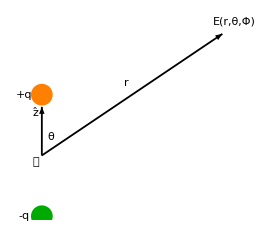

The field for the magnetic dipole is far more tedious to calculate as we have seen, since there are more vectors involved. The two examples appear to be unrelated, but in fact they are intimately related.

-Graphics3D-

2.6 Comparing the Electric and Magnetic Dipoles

In this section we are going to explore why the electric and magnetic dipole fields of an ideal dipole must have exactly the same coordinate dependence. It serves as a great intuitive example of why E and B are twins, in spite of the fact that they may look totally unrelated. The dipole is an exceptionally important source that appears throughout electrodynamics and everywhere in the real world.

Consider the function

(ẑ)/r=(ẑ)/(√(x^2+y^2+z^2))

In what follows, we shall stay away from r = 0. The significance of this is apparent: an ideal dipole is defined to be one which is so small that you can never get close to it. Calculate the curl.

(∇×(ẑ)/r)_i=ϵ_ij3∂_j 1/(r_n r_n)^(1/2)=-ϵ_ij3 r_j/r^3=((ẑ ×  r)/r^3)_i

Calculate ∇×(ẑ)/r.

```mathematica
ClearAll["Global`*"]; A =Curl[1/(√(x^2+y^2+z^2)){0,0,1},{x,y,z}]
```

{-y/((x^2+y^2+z^2)^(3/2)),x/((x^2+y^2+z^2)^(3/2)),0}

Transform to spherical coordinates.

```mathematica
TransformedField["Cartesian"->"Spherical",A,{x,y,z}->{r,θ,ϕ}] // FullSimplify; Simplify[%,{r>0}]
```

{-y/((x^2+y^2+z^2)^(3/2)),x/((x^2+y^2+z^2)^(3/2)),0}

This is a vector function that makes circles in the x-y plane. It turns out to have the EXACT coordinate dependence of the vector potential of an ideal dipole. The reason for this is that the source of the ideal magnetic dipole is a tiny current loop. The vector A points in the same direction as J

A=(("μ")_0)/(4π)∫ 𝕕𝕍' J/ℛ

and the curl of a vector that is circular and has 1/r dependence gives A.

Plot in 3D.

```mathematica
StreamPlot3D[A,{x,-1,1},{y,-1,1}, {z,-1,1}]
```

-Graphics3D-

If we take a second curl, this gives the coordinate dependence of the dipole field.

Calculate  ∇×(∇×(ẑ)/r).

```mathematica
B =Curl[A,{x,y,z}]
```

{(3 x z)/((x^2+y^2+z^2)^(5/2)),(3 y z)/((x^2+y^2+z^2)^(5/2)),-(3 x^2)/((x^2+y^2+z^2)^(5/2))-(3 y^2)/((x^2+y^2+z^2)^(5/2))+2/((x^2+y^2+z^2)^(3/2))}

In spherical coordinates,  you will recognize this function as the dipole coordinate dependence.

Transform to spherical coordinates.

```mathematica
TransformedField["Cartesian"->"Spherical",B,{x,y,z}->{r,θ,ϕ}] // FullSimplify
```

{(2 Cos[θ])/((r^2)^(3/2)),Sin[θ]/((r^2)^(3/2)),0}

Plot in 3D.

```mathematica
StreamPlot3D[B,{x,-1,1},{y,-1,1}, {z,-1,1}]
```

-Graphics3D-

If we take another curl we must get zero (away from source).

∇×B=μ_0 J=0	r≠0

Calculate  ∇×[∇×(∇×(ẑ)/r)].

```mathematica
FullSimplify[Curl[B,{x,y,z}]]
```

{0,0,0}

Take the divergence of our function.

∇\[Application](ẑ)/r=-(ẑ \[Application] r)/r^3=-cosθ/r^2

Calculate  the divergence.

```mathematica
div=Div[1/(√(x^2+y^2+z^2)){0,0,1},{x,y,z}]
```

-z/((x^2+y^2+z^2)^(3/2))

Put this result in spherical variables.

```mathematica
$Assumptions=r>0;xxx=TransformedField["Cartesian"->"Spherical",div,{x,y,z}->{r,θ,ϕ}] // FullSimplify
```

-Cos[θ]/r^2

This you will recognize as having the EXACT coordinate dependence of the scalar potential for an electric dipole.  Just as its curl was a circular vector, its divergence is just a cosine and they have the same r dependence. A scalar function is ironically harder to visualize than a vector function. For a vector function we can just plot arrows in space. For a scalar function, arrows are be replaced by numbers and that has no visualisation . For a scalar function, usually we take a slice, in this case we may choose y = 0, and plot the scalar function as the height in an x-z plot. You can see the plot has singularities where the charges would be located and obviously has an r and θ dependence.

```mathematica
Plot3D[z/((x^2+z^2)^(3/2)),{x,-1,1},{z,-1,1},PlotRange->All]
```

-Graphics3D-

Now consider the vector identity (true for any vector).

∇×(∇×(ẑ)/r)=∇(∇\[Application](ẑ)/r)-∇^2 (ẑ)/r

The last term you will recognize as a Dirac delta function. It is zero as long as r is not zero. We can rewrite it as

∇×(∇×(ẑ)/r)=-∇(-∇\[Application](ẑ)/r)

The left side gives the coordinate dependence of an ideal magnetic dipole (first curl gives A and second gives B). The right side gives the coordinate dependence of an ideal electric dipole (divergence gives V and negative gradient gives E). And this is how in the simplest and most physically intuitive way, you can see why the fields of electric and magnetic ideal dipoles must have the same coordinate dependence.

∇×(∇×(ẑ)/r)=(3(r̂\[Application]ẑ)r̂- ẑ)/((r^3)^)=-∇(-∇\[Application](ẑ)/r)

V=1/(4π ε_0)(p\[Application]r̂)/((r^2)^)		E=-∇V=1/(4π ε_0)(3(r̂\[Application]p)r̂- p)/((r^3)^)		p=p ẑ

A=μ_0/(4π)(m ×r̂)/((r^2)^)			B=∇×A=μ_0/(4π)(3(r̂\[Application]m)r̂- m)/((r^3)^)		m=m ẑ

2.7 Expansion of A and the Magnetic Dipole

Recall we singled out the electric dipole for its important role in nature. The same is true of the magnetic dipole. A physical magnetic dipole consists of a small loop carrying a steady current. In Chapter 1, we expanded 1/ℛ in terms of Legendre polynomials to get the multipole expansion for V. We can do the same thing for A.

A=(("μ")_0)/(4π)∮ ℐ/ℛ ⅆ𝕝'=(("μ")_0ℐ)/(4π r) ∮ ⅆ𝕝' +(("μ")_0ℐ)/(4π r^2)∮ r' P_1(cosα)ⅆ𝕝' +(("μ")_0ℐ)/(4π r^3)∮ r'^2 P_2(cosα)ⅆ𝕝'+...

The leading term is zero. The next term, the dipole may be written

A_dip=(("μ")_0ℐ)/(4π r^2)∮ r' P_1(cosα)ⅆ𝕝' =(("μ")_0ℐ)/(4π r^2)∮ r̂\[Application]r' ⅆ𝕝'  =(("μ")_0ℐ)/(4π r^2)∫ ⅆ𝕒'×r̂

where the last step will be proved below. The magnetic dipole vector is defined as

m=ℐ∮ ⅆ𝕒'

which gives

A_dip=(("μ")_0m×r̂)/(4π r^2)

Now we prove the vector identity

∮ r̂\[Application]r' ⅆ𝕝  =∫ ⅆ𝕒'×r̂

The technique is to multiple by a constant vector C which facilitates the use of Stoke’s theorem. The calculation is made vastly easier using index notation.

∮d𝕝_j'(C_j (r̂)_i r_i')=∫ (ⅆ𝕒)_j' ϵ_jik∂_j '(C_k (r̂)_p r_p')= ∫ (ⅆ𝕒)_j' ϵ_jik C_k (r̂)_i=C_k∫ ϵ_kji(ⅆ𝕒)_j' (r̂)_i

Calculate the field due to a magnetic dipole.

```mathematica
Curl[(Subscript[μ, 0] Sin[θ])/(4π r^2)m{0,0,1},{r,θ,ϕ},"Spherical"]
```

{(m Cos[θ] μ_0)/(2 π r^3),(m Sin[θ] μ_0)/(4 π r^3),0}

2.8 Boundary Conditions

The normal component of a magnetic field is continuous at any boundary.

(B^⊥)_above=(B^⊥)_below

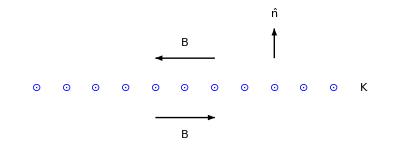

```mathematica
Graphics[{Table[{Blue,Style[Text["⊙",{i,0}],18]},{i,0,10}],Arrow[{{6,1},{4,1}}],Style[Text["B",{5,1.5}],18,Bold],Arrow[{{4,-1},{6,-1}}],Style[Text["B",{5,-1.6}],18,Bold],Style[Text["K",{11,0}],18,Bold],Style[Text[n̂,{8,2.5}],18,Bold],Arrow[{{8,1},{8,2}}],}]
```

The tangential component of a magnetic field is discontinuous when there is a surface current.

(B^‖)_above-(B^‖)_below=μ_0 K

The boundary conditions may be combined into a single vector equation

B_above-B_below=μ_0 K×n̂

2.9 Helmholtz Coils

The Helmholtz coil configuration consists of 2 current loops (or perhaps very short solenoids) of radius R separated by a distance d. The current vector is identical for each loop. A careful choice of d produces a remarkably uniform field between the coils.

```mathematica
Graphics3D[{Style[Text[R,{.2,.5,0}],12],Style[Text[d,{-1.2,0,0.5}],12],Line[{{0,0,0},{0,1,0}}],Line[{{-1,0,0},{-1,0,1}}],Orange, Opacity[0.3],Thickness[0.01],Opacity[.7],ResourceFunction["Circle3D"][{0,0,0},{1,1},π/2],ResourceFunction["Circle3D"][{0,0,1},{1,1},π/2]},Boxed->False]
```

-Graphics3D-

The magnetic field is that of the superposition of the 2 loops. On axis at a distance z from the center, the result is

B=(R^2 ℐ μ_0)/((2 [R^2+(d/2+z)^2])^(3/2))+(R^2 ℐ μ_0)/((2 [R^2+(d/2-z)^2])^(3/2))

At the center (z = 0), the field is maximum and its derivative is zero.

Calculate the derivative of the magnetic field with respect to z at the center.

```mathematica
FirstDerivative=D[(R^2 ℐ Subscript[μ, 0])/(2 (R^2+(d/2+z)^2)^(3/2))+(R^2 ℐ Subscript[μ, 0])/(2 (R^2+(d/2-z)^2)^(3/2)),z] ;
FirstDerivative/. z->0
```

0

Finding the zero of the second derivative at the center as a function of current loop separation gives the optimum value for d to  make a uniform field at the center.

Calculate the second derivative of the magnetic field with respect to z at the center.

```mathematica
SecondDerivative=D[FirstDerivative,z] /. z->0
```

(15 d^2 R^2 ℐ μ_0)/(4 (d^2/4+R^2)^(7/2))-(3 R^2 ℐ μ_0)/((d^2/4+R^2)^(5/2))

Find the coil separation for which the second derivative is zero at the center.

```mathematica
Solve[SecondDerivative==0,d]
```

{{d→-R},{d→R}}

The choice d = R is the Helmholtz coil configuration.

Calculate the field at the center for R=.1  "m" and ℐ=10  "A".

```mathematica
ClearAll["Global`*"];R=.1 Quantity[, "Meters"]; ℐ=10 Quantity[, "Amperes"]; z=0 Quantity[, "Meters"]; UnitConvert[(R^2 ℐ Quantity[, "MagneticConstant"])/(2 (R^2+(R/2+z)^2)^(3/2))+(R^2 ℐ Quantity[, "MagneticConstant"])/(2 (R^2+(R/2-z)^2)^(3/2)),Quantity[, "Teslas"]]
```

0.0000899176 T

Calculate the field at z = 1 cm.

```mathematica
z=0.01 Quantity[, "Meters"];UnitConvert[(R^2 ℐ Quantity[, "MagneticConstant"])/(2 (R^2+(R/2+z)^2)^(3/2))+(R^2 ℐ Quantity[, "MagneticConstant"])/(2 (R^2+(R/2-z)^2)^(3/2)),Quantity[, "Teslas"]]
```

0.0000899074 T

2.10 Summary of B, A, and J

Here is a summary of how to calculate one quantity from another in magneto-statics. The hardest conversion to do is to get A from B because there is no easy recipe for undoing a curl. See, for example, Section 2.5.

J→ B            B=(("μ")_0)/(4π)∫(J×ℛ)/ℛ^3 ⅆ𝕍'

B→J    	∇×B=  ("μ")_0J

A→B             B =∇×A

B→A             ∫ B\[Application] ⅆ𝕒=∮  A \[Application] ⅆ𝕝

J→ A             A=(("μ")_0)/(4π)∫(J(r))/ℛ ⅆ𝕍'

A→ J             J=-1/(("μ")_0)∇^2 A

Exercises

Consider a current loop in the shape of a regular polygon with n sides. Find the minimum value of n such that the field at the center is within 1% of that for a circle of radius equal to the perpendicular distance from the polygon center to any side.

Consider a square loop of side a in the x-y plane with clockwise current ℐ. At a distance r in the plane of the current loop, perpendicular to two of the sides,
a) What is the direction of B ?
b) Determine the magnetic field for r  > a (exact solu tion).
c) Find a simple expression for the magnetic field in the limit r >> a.
Hint: The contribution from the vertical sides is NOT zero.

A thick slab extending from z = −a to z = +a (and infinite in the x and y directions) carries a volume current J = (J_0z^2/A)x̂ . Find the magnetic field, as a function of z, both inside and outside the slab.

A cone with a circular base has a uniform surface charge density σ on both the curved side an flat bottom. The height is d and the cone angle is θ. The cone spins about its axis counter-clockwise with constant ω, as viewed from the tip. Calculate the magnetic field at the tip of the cone

Consider a wire of 1 mm radius that carries a current of 1 A.
a) Estimate the “drift speed” speed of an electron assuming that the number of conduction electrons per volume is 1 per atom.
b) Calculate the radial electric field needed to cancel the magnetic force on the electrons at a distance r (inside the wire) from the center of the wire.
c) c) How many extra electrons are needed, per meter of wire length, to cancel the magnetic field at a distance r from the center of the wire?
d) d) Use these numbers to reason that the current is uniform per area in the wire.